```mathematica
fs=FullSimplify;ft=Flatten;nls=Normal[Series[#1,#2]]&;po=PowerExpand;Θ=HeavisideTheta;
AS=ApplySides;MGF=MomentGeneratingFunction;PGF=FactorialMomentGeneratingFunction;
```

### Probabilistic argument

define the events
EST: the WT establishes in host k
SV: a lineage destined to establish in k is produced during growth of WT in j by mutation from WT
DN: a lineage destined to establish in k is produced during decay of WT in k by mutation from WT
INF: successful infection occurs from host j to host k

an ER lineage is a lineage produced by mutation from the WT, that is destined to establish in the target host k

failed infection occurs iff 
(i) the inoculated WT does not establishes in host k: OverBar[EST]
AND
(ii) the WT does not produce any ER lineage during its growth in host j: OverBar[SV]
AND
(iii) the WT does not produce any ER lineage during its decay in host k: OverBar[DN]

we can write:

OverBar[INF] = OverBar[EST] ∩OverBar[SV]∩OverBar[DN]

SV is independent of ES and DN  :ℙ[OverBar[INF]] =ℙ[OverBar[SV]]ℙ[OverBar[DN]∩OverBar[EST]]
DN depends on EST : the probability of OverBar[DN] is computed under the condition that OverBar[EST] 
ℙ[OverBar[DN]∩OverBar[EST]]=ℙ[OverBar[DN]|OverBar[EST]]ℙ[OverBar[EST]]

ℙ[OverBar[INF]] =ℙ[OverBar[EST]]ℙ[OverBar[SV]]ℙ[OverBar[DN]|OverBar[EST]]

### Establishment in plant : EST under Feller approx

#### Feller approximation for infectious process

assumptions:feller limit (can be shown to emerge from large Ν_0 limit rigorously)
⇒ two feller coefs: r_i for type i and σ_i as in martin et al 2013
Θ=heaviside theta function
ρ=r/σ =(growth rate)/(demographic noise rate) ratio
establishment proba of a single copy mutant :  π[ρ]=Θ[ρ](1-ⅇ^(-2ρ))≈_(0<ρ<<1)2ρ

discrete time + poisson offspring nb distribution ⇒ feller coefs :r_i, σ=1 ⇒ρ_i=r_i

BD process  ⇒ feller coefs :r_i=b_i-d_i, σ_i=b_i+d_i  exact π[ρ]=Θ[ρ](2ρ)/(1+ρ), feller approx π[ρ]≈Θ[ρ](1-ⅇ^(-2ρ))

(2 ρ)/(1+ρ)

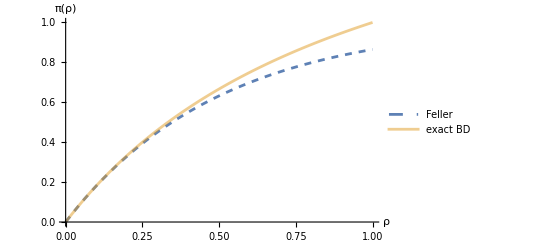

```mathematica
1-d/b/.ft[Solve[{b-d==ρ σ,b+d==σ},{b,d}]]//fs
Plot[{1-ⅇ^(-2ρ),%},{ρ,0,1},PlotLegends->{"Feller","exact BD"},PlotStyle->{Dashed,Opacity[0.5]},AxesLabel->{ρ,π[ρ]}]
```

#### Example: Feller coefs for a burst - death model with recurrent bottlenecks

consider  the  Burst - death  model  (Hubbarde  et  al  2007)
its PGF G[x,t] is solution of

-Graphics-

-Graphics-

-Graphics-

#### host specific demographic variance during infection

we assume that uin host k the infection process implies stochastic variance σ_k (independent of types)
this  σ_k is due generated by the complex process of infection within cells and succesive bottlenecks acrosss cells
baded on Wahl & Gerrish 2001 we conjecture that this boils down to a genotype indep σ_k for host k
the establishment proba per inoculated virion under the feller approx is :π[x_i,k]=Θ[r[x_i,k]](1-ⅇ^(-2 r[x_i,k]/σ_k))
σ_k and r[x_i,k] are homogeneous to rates per unit time (eg per hour)
we scale time by the maximal possible growth rate in host k: r_max[k]>0

r[x,k]=r_max[k](1-(x-o_k)^2/R_k^2)  
establishment proba:
π[x,k]=1-ⅇ^(-2 ξ_k ρ[x,k]) where
 ρ[x,k]=r[x,k]/r_max[k]=1-(x-o_k)^2/R_k^2 is a scale free  host k * type x specific growth rate 
 ξ_k=r_max[k]/σ_k is a scale-free host specific demographic variance (in rescaled time)

#### Infection by establishment from an inoculum with “target inoculabilition proba” p_k

* sampling of Ν_0 copies from source (fixed across source species) 
* each with proba p_k to successfully infect target k
* Ν_0>>1 and p_k<<1 poisson limit: n_(0,k)\[Distributed]Poisson[N_0 p_k] sucessful infections

after inoculation of n_(0,k)virions,each having independent establishment proba π[j,k](branchingproperty)
the proba of establishment from all copies inoculated from source j in host k is:
ℙ_EST[j,k]=𝔼_(n_(0,k))[1-(1-π[j,k])^(n_(0,k))]
we have : π[j,k]=1-ⅇ^(-2 ξ_k r_(j,k)^*)

let q_k=Ν_0 p_k ξ_k=O[1] while Ν_0>>1, p_k<<1 and ξ_k<<1
to leading order the probability of at least one establishment is:

ℙ[EST]=1-ℙ[OverBar[EST]]=ℙ_EST[j,k]=𝔼_(n_(0,k))[1-(1-π[j,k])^(n_(0,k))] ~  Θ[r_jk](1-ⅇ^(-2 q_k r_jk))(1+o[ϵ])
q_k=Ν_0 p_k ξ_k
Θ[.]:heaviside theta function

```mathematica
conds=Subscript[n, 0,k]>0&&Subscript[Ν, 0]>0&&0<Subscript[p, k]<1&&Subscript[q, k]>0&&Subscript[r, jk]∈Reals&&Subscript[ξ, k]>0;
Expectation[1-(1-Subscript[π, jk])^Κ,Κ\[Distributed]PoissonDistribution[Subscript[Ν, 0] Subscript[p, k]]]
fs[%/.Subscript[π, jk]->Θ[Subscript[r, jk]](1-ⅇ^(-2 Subscript[r, jk] Subscript[ξ, k])),conds&&#]&/@{Subscript[r, jk]<0,Subscript[r, jk]>0}
1-Exp[nls[Log[1-%]/.{Subscript[ξ, k]->ϵ Subscript[ξ, k],Subscript[Ν, 0]->Subscript[Ν, 0]/ϵ,Subscript[p, k]->Subscript[p, k] ϵ},{ϵ,0,1}]/.Subscript[ξ, k]->Subscript[q, k]/(Subscript[Ν, 0] Subscript[p, k])]//po//fs
```

1-ⅇ^(-p_k π_jk Ν_0)

{0,1-ⅇ^((-1+ⅇ^(-2 r_jk ξ_k)) p_k Ν_0)}

{0,1-ⅇ^(-2 ϵ q_k r_jk)}

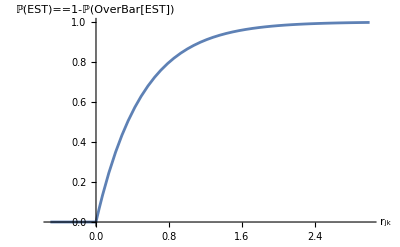

```mathematica
Plot[Θ[Subscript[r, jk]](1-ⅇ^(-2 Subscript[q, k] Subscript[r, jk]))/.Subscript[q, k]->1,{Subscript[r, jk],-0.5,3},AxesLabel->{Subscript[r, jk],ℙ[EST]==1-ℙ[OverBar[EST]]}]
```

### Mutation and fixation process

#### linear approx of π[i,k] (ξ_k r<<1)

mean establishment proba of mutants from clone j in host k
π[j,k]=Θ[r_(j,k)^*](1-ⅇ^(-2 ξ_k r_(j,k)^*))
1-ⅇ^(-2 ξ r)≈_(ξ r<<1)2 ξ r
π[j,k]≈2 ξ_k r_(j',k)^*
averaged over the distribution of mutant growth rates:
Π[j,k] =𝔼[Θ[r_(j',k)^*]r_(j',k)^*|parent j] 
determined by the fitness landscape
π̄[j,k]=𝔼_j'[π[j',k]]≈2 ξ_k Π[j,k]

```mathematica
nls[1-ⅇ^(-2 x),{x,0,1}]
```

2 x

#### mutation process (general)

consider mutations from type i to type i', occuring in host j, and destined to estabish in target host k

they are produced as a poisson process with rate U_i[k] n_i[t,k] 𝒻_(x_i->x_i') π[i',k]ⅆt per unit time (arbitrary units)
π[i,k]≈2 ξ_k Θ[r_(i,k)^*]r_(i,k)^*: establishment proba of mutant i in host k
n_i[t,k] : size of parental clone i in host k at time t

𝒻_(x_i->x_i'): transition proba upon mutation, from type i (x_i) to type  i'  (x_i'),assumed constant across hosts

U_i[k]: (scale free) mutation rate per k-specific rescaled unit time for parent i

#### constant mutation rate across hosts and types

with a birth death process : U_i[k]=(b_i[k]u[k])/r_max[k] where 
b_i[k] is a net birth rate of type i in host k 
u[k] is mutation proba per divsion in host k
* assume that b_i[k]=α r_max[k] (1+β_i)(same time scaling)  where the β_i are independent of k (single fitness landscape)

* assume that u[k] =u is constant across hosts (inherent to the viral species and the infectious process within plant host cells)
then  U[k]=α u (1+β_i)

* assume that β_i (relative effects on birth rates) are small:β_i=O[ϵ^κ] for some order κ>0
then U[k]=α u (1+β_i)=α u(1+o[1])
U[k]≈U is a constant rate of mutation per rescaled time units

```mathematica
(Subscript[b, i][k]u[k])/(Subscript[r, max][k])/.u[k]->u/.Subscript[b, i][k]->α Subscript[r, max][k](1+Subscript[β, i])
%/.u->u ϵ/.Subscript[β, i]->Subscript[β, i] ϵ^κ//fs
Limit[%/(α u ϵ),ϵ->0,Assumptions->κ>0]
```

u α (1+β_i)

u α ϵ (1+ϵ^κ β_i)

1

#### Production of mutants during growth or decay : Feller ⇒ IG

in ref below r=δ and σ=β^2 and BM=BrownianMotion
Y\[Distributed]BM[r,σ]⇒ First passage time τ from W_0=0 to W_τ=A>0 
τ\[Distributed]IG[μ,λ] where μ=A/r and λ=A^2/σ

```mathematica
fs[PDF[InverseGaussianDistribution[μ,λ],x],x>0]
```

(ⅇ^(-(λ (x-μ)^2)/(2 x μ^2)) √(λ/x^3))/(√(2 π))

-Graphics-

-Graphics-

Z_t\[Distributed]Feller[r,σ] ⇒ SDE: dZ_t=r Z_t dt+√(v Z_t)dB_t
Lamperti Transform Y defined by Y_(∫_0^t Z_v ⅆv)=Z_t for all t
dZ_t=r dt+√v dB_t ⇒ Y_τ\[Distributed]BM[r,v]
from initial value (t=τ=0) Y_0=Z_0 to  final value (t=T,τ=∫_0^T Z_v ⅆv ) Y_τ=Z_T

⇒τ=∫_0^T Z_v ⅆv is the cumulative size from 0 to T 
⇒ τ is also the first passage time of a BM[r,v] from Y_0=Z_0 to Y_τ=Z_T

it is equivalently the first passage time from Y_0=0 to Y_τ=Z_T-Z_0
source host :Z_t\[Distributed]Feller[1,1/ξ_j] ,positive growth from Z_0=1 to Ν 
Y_τ\[Distributed]BM[1,1/ξ_j] goes from Y_0=0 to Y_S=Ν-1.08≈Ν
S_j\[Distributed]IG[Ν,Ν^2 ξ_j]

target host | decay: we take the reverse time process t_-=-t
if r<0 then Z_(t_-)\[Distributed]Feller[-r_jk^*,1/ξ_k]=Feller[|r_jk^*|,1/ξ_k]
if r>=0 and + conditionned on Z_∞=0 then :
Z_t|Z_∞=0\[Distributed]Feller[-|r_jk^*|,1/ξ_k]⇒Z_(t_-)|Z_∞=0\[Distributed]Feller[|r_jk^*|,1/ξ_k]

Z_(t_-) goes from Z_∞=0 to Z_0=n_0

and thus 
Y_(τ-)\[Distributed]BM[|r|,σ]goes from Y_0=0 to Y_(τ_-)=n_0>0
S_k\[Distributed]IG[n_0/(|r_jk|),n_0^2 ξ_k]

```mathematica
MGF[InverseGaussianDistribution[V/r,V^2 Subscript[ξ, k]],-z]
```

ⅇ^(r V (1-√(1+(2 z)/(r^2 ξ_k))) ξ_k)

### No Infection by rescue in target : OverBar[DN]

mutation rate to type j': u_j'=U ℙ[j->j']
probability that it establishes: π_j'k≈𝟙[r_j'k]2 ξ_k r_j'k
by the property of poisson processes 
summed over all possible types:U_ER=∑_j' u_j' π_j'k->2U ξ_k Π_jk
total nb of ER lineages is Poisson process with intensity 
𝓃_jk[t]ξ_k ν where  ν=2U ξ_k Π_jk

so that by the time of extinction: 
n_ER|S_k\[Distributed]Poisson[S_k ξ_k ν]

let ξ=ξ_k and S=S_k and ν=2U ξ_k Π_jk
ℙ[no ER lineage produced ]
ℙ[OverBar[DN]|OverBar[EST],S]=ⅇ^(-S ν ξ)

taking expectation on S_k|V_jk \[Distributed] IG[V_jk/r,V_jk^2 ξ_k] where r=|r_jk|

then on V_jk \[Distributed]Poisson[Λ p_k]
yields: 
ℙ[OverBar[DN]|OverBar[EST]]=ⅇ^(-Λ p_k(1-ⅇ^(-r ξ(√(1+(2 ν)/r^2)-1))))

```mathematica
PGF[PoissonDistribution[ν ξ S],0]
Expectation[%,S\[Distributed]InverseGaussianDistribution[Subscript[V, jk]/r,Subscript[V, jk]^2 ξ]];
fs[Expectation[%,Subscript[V, jk]\[Distributed]PoissonDistribution[Λ Subscript[p, k]]]//po,ξ>0&&Λ>0&&0<Subscript[p, k]<1]
P0=ⅇ^(-Λ Subscript[p, k](1-ⅇ^-λ))/.λ->ξ(√(r^2+2 ν)-r);
fs[P0==%%//po,r>0&&ξ>0&&Λ>0&&0<Subscript[p, k]<1]
```

ⅇ^(-S ν ξ)

ⅇ^((-1+ⅇ^(r (ξ-√(1+(2 ν)/r^2) ξ))) Λ p_k)

True

we have : λ=r ξ(√(1+(2 ν)/r^2)-1)(->)_(ξ  ->  0)0
so we can take an approx: -Log[P0]=(1-ⅇ^-λ) Λ p_k≈λ Λ p_k+o[ϵ]
which yields:

ℙ[OverBar[DN]|OverBar[EST]]≈Exp[-(√(r^2+2 ν)-r) q_k]
where 
r=|r_jk^*|  and ν=2 U^* Π_jk and q_k=Λ p_k ξ_k

```mathematica
Exp[-(√(r^2+2 ν)-r) Subscript[q, k]]==Exp[nls[Log[P0],{ξ,0,1}]/.Λ->Subscript[q, k]/(Subscript[p, k] ξ)//po//fs]//fs
```

True

### No Infection by rescue from the source: OverBar[SV] & OverBar[EST]

#### General description of inoculum from source host (WT + mutants)

WT or parent lineage is j
𝒻_j':frequency of mutant lineage j' from parent j under indefinite growth in the source
inoculate V\[Distributed]Poisson[Λ] virions in total on the plant
harsh dilution by some factor p_k<<1 characteristic of the host
F=∑_j' 𝒻_j' :total frequency of mutants in the plant
1-F: frequency of the WT in the plant
SSWM= F<<1 : WT is dominant overall in the source⇒1-F->1
the nb of virions  of type j that enter the host is V_jk\[Distributed]Poisson[Λ p_k]

```mathematica
Expectation[PGF[BinomialDistribution[V0,Subscript[p, k]],z],V0\[Distributed]PoissonDistribution[Λ]]==PGF[PoissonDistribution[Λ Subscript[p, k]],z]
```

True

#### Failed WT establishment : ℙ[OverBar[EST]]

nb of j virions that enter the plant:V_jk\[Distributed]Poisson[Λ p_k]
each copy if j produces an infection with proba :π_jk=Θ[r_jk^*](1-ⅇ^(-2 ξ_k r_jk^*))
the whole WT sample produces no infection with proba: ℙ[OverBar[EST]|Ν]=(1-π_jk)^V_jk
deconditionning on distibution of Ν|V then on V :
ℙ[OverBar[EST]]=𝔼_V_jk[(1-π_jk)^V_jk]=ⅇ^(-Λ p_k π_jk)
assume ξ_k r_jk^*<<1 or r_jk<0  ⇒π_jk≈Θ[r_jk^*]2 ξ_k r_jk^* and :
ℙ[OverBar[EST]]≈ⅇ^(-2 (1-F) q_k r_jk)⇒_(SSWM=F<<1)ℙ[OverBar[EST]]≈ⅇ^(-𝟙_+[r_jk] 2 q_k r_jk)
where q_k=Ν p_k ξ_k

```mathematica
conds=0<Subscript[p, k]<=1&&Ν>0&&0<=𝒻<1&&0<F<=1;
Expectation[(1-Subscript[π, jk])^Subscript[V, jk],Subscript[V, jk]\[Distributed]PoissonDistribution[Ν Subscript[p, k]]]//fs
%/.Subscript[π, jk]->𝟙[Subscript[r, jk]]2 Subscript[ξ, k] Subscript[r, jk]/.Subscript[ξ, k]->Subscript[q, k]/(Ν Subscript[p, k])
```

ⅇ^(-Ν p_k π_jk)

ⅇ^(-2 q_k r_jk 𝟙[r_jk])

#### number of mutants in the sample and ℙ[OverBar[SV]_j'|m_j']

𝓂_j'∈ℕ: nb of segregating copies of type j' mutant in a source population of size Ν (𝒻_j'=𝓂_j'/Ν)
the total sample size is V \[Distributed]Binomial[Ν,p_k]->Poisson[Ν p_k]
the sampled virion is a mutant j' with proba 𝒻_j':V_j'k|V\[Distributed]Binomial[V,𝓂_j'/Ν]
⇒V_j'k\[Distributed]Poisson[p_k 𝓂_j']

```mathematica
Expectation[PGF[BinomialDistribution[V,Subscript[𝓂, j']/Ν],z],V\[Distributed]PoissonDistribution[Ν Subscript[p, k]]]==PGF[PoissonDistribution[Subscript[𝓂, j'] Subscript[p, k]],z]//fs
```

True

any of the V_j'k mutant copy that enters establishes in host k with probability π_j'k=Θ[r_j'k^*](1-ⅇ^(-2 ξ_k r_j'k^*))
no such establishment happens with proba ℙ[OverBar[SV]_j'|m_j']=𝔼_(V_j'k|m_j')[(1-π_j'k)^V_j'k]=ⅇ^(-p_k π_(k j') 𝓂_j')

```mathematica
Expectation[(1-Subscript[π, j'k])^Subscript[V, j'k],Subscript[V, j'k]\[Distributed]PoissonDistribution[Subscript[𝓂, j'] Subscript[p, k]],Assumptions->0<=Subscript[𝓂, j']<=Ν&&0<Subscript[p, k]<1&&0<Subscript[π, j'k]<1]
```

ⅇ^(-p_k π_(k j') 𝓂_j')

#### distribution of m_j' : ℙ[OverBar[SV]_j'|S_j,𝓂]

ℙ[OverBar[SV]_j'|m_j']=ⅇ^(-p_k π_(k j') 𝓂_j')
by the branching property there is independent estblishment  for distinct mutants 
conditional on the set m={ m_j'}_j' of mutant copy numbers over all possible mutants:
ℙ[OverBar[SV]|m]=∏_j' ℙ[OverBar[SV]_j'|𝓂_j']=∏_j' ⅇ^(-p_k π_(k j') 𝓂_j')

The law of the production of mutants is independent of mutant type and each type has iid  copy number
The distribution of mutant copy numbers is 
𝓂_j'|S_j=B_j 𝓂 where  Piecewise[{{B_j'\[Distributed]Bernoulli(1-ⅇ^(-S_j u_j' π_j'j)), □}, {𝓂 \[Distributed] 𝒟, □}}]
where 𝓂 is the law of mutant copy numbers if it appears in the growth phase, independent of the type j'

we assume that by the end of the infection stochastic demography is more limited than when invading a new uninfected plant
therefore π_j'j≈1 for all mutants of the clone j that is optimal in that plant

ℙ[OverBar[SV]_j'|S_j,𝓂]=ⅇ^(-π_(j j') S_j u_j')+ⅇ^(-𝓂 p_k π_(k j')) (1-ⅇ^(-π_(j j') S_j u_j'))

```mathematica
ℙ[Subscript[OverBar[SV], j'],𝓂,Subscript[S, j]]=Expectation[ⅇ^(-Subscript[p, k] Subscript[π, k j'] Subscript[𝓂, j'])/.Subscript[𝓂, j']->𝓂 Subscript[B, j'],Subscript[B, j']\[Distributed]BernoulliDistribution[1-ⅇ^(-Subscript[S, j] Subscript[u, j'] Subscript[π, j'j])]]/.Subscript[π, j'j]->1
```

ⅇ^(-S_j u_j')+ⅇ^(-𝓂 p_k π_(k j')) (1-ⅇ^(-S_j u_j'))

#### Deconditioning on S_j:ℙ[OverBar[SV]_j'|𝓂]

we have S_j\[Distributed]InverseGaussianDistribution[Ν,Ν^2 ξ_j] independent of 𝓂
ℙ[OverBar[SV]_j'|𝓂]=𝔼_S_j[ℙ[OverBar[SV]_j'|S_j,𝓂]]=ⅇ^-θ+ⅇ^-α (1-ⅇ^-θ)
where α=Ν ξ_j(√(1+(2 u_j')/ξ_j)-1)
and:θ=𝓂 p_k π_(k j')

```mathematica
conds=𝓂 >=1&&0<Subscript[p, k]<=1&&0<= Subscript[π, k j']<1&&Subscript[u, j']>0&&Subscript[ξ, j]>0;
ℙ[Subscript[OverBar[SV], j'],𝓂]=fs[Expectation[ℙ[Subscript[OverBar[SV], j'],𝓂,Subscript[S, j]],Subscript[S, j]\[Distributed]InverseGaussianDistribution[Ν,Ν^2 Subscript[ξ, j]],Assumptions->conds]//po,conds]
fs[ℙ[Subscript[OverBar[SV], j'],𝓂]==ⅇ^-θ+ⅇ^-α (1-ⅇ^-θ)/.{θ->𝓂 Subscript[p, k] Subscript[π, k j'],α->(√(1+(2 Subscript[u, j'])/Subscript[ξ, j])-1) Ν Subscript[ξ, j]}//po,conds]
```

ⅇ^(-𝓂 p_k π_(k j'))+ⅇ^(Ν (ξ_j-√(ξ_j (2 u_j'+ξ_j))))-ⅇ^(-𝓂 p_k π_(k j')+Ν ξ_j-Ν √(ξ_j (2 u_j'+ξ_j)))

True

#### Continuous type limit: ℙ[OverBar[SV]|𝓂]

with a continuous distribution of types :
u_j'=U ℙ[j->j']->U 𝒻_k[r,j]ⅆr->0
where 𝒻_k[r,j]=PDF of mutant r from in host k from parent j
Log[ℙ[OverBar[SV]_j',𝓂]]=u_j' Ν(1-ⅇ^(-𝓂 p_k π_(k j')))≈-𝓂 Ν p_k π_(k j') u_j'
then taking the product of all type's contributions:

Log[ℙ[OverBar[SV],𝓂]]=∑_j' Log[ℙ[OverBar[SV]_j',𝓂]]=-𝓂 ν q_k
with 
ν=2 U Π_jk 
 Π_jk=∑_j' (π_(k j')ℙ[j->j'])/(2 ξ_k)->∫_0^1 r f_k[r,j]ⅆr
q_k=Ν p_k ξ_k

```mathematica
-Subscript[u, j']Limit[-Log[ℙ[Subscript[OverBar[SV], j'],𝓂]]/Subscript[u, j'],Subscript[u, j']->0,Direction->"FromAbove",Assumptions->conds]
nls[%/.Subscript[p, k] Subscript[π, j' k]->ϵ,{ϵ,0,1}]/.ϵ->Subscript[p, k] Subscript[π, j' k]/.Subscript[u, j']->U Subscript[f, j']
%/.ft[Solve[{Subscript[Π, jk]==(Subscript[f, j'] Subscript[π, j'k])/(2 Subscript[ξ, k]),ν==2U Subscript[Π, jk],Subscript[q, k]==Ν Subscript[p, k] Subscript[ξ, k]},{Subscript[f, j'],U,Ν}]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-((Ν-ⅇ^(-𝓂 p_k π_(k j')) Ν) u_j')

-U 𝓂 Ν f_j' p_k π_(k j')

-𝓂 ν q_k

### MGFs of 𝓂

#### Pure burst model with a cost (+ large burst size limit)

-Graphics-

fixed burst size :R=B+1⇒ f[z]=𝔼[z^R]=z^(B+1)
solution P[z,t]=𝔼[z^n_t]=(1+ⅇ^(B λ t)(z^-B-1))^(-1/B)

```mathematica
conds=B>0&&λ>0&&0<z<1&&t>=0&&z>=0&&0<=c<1&&τ>0&&X>=0&&ρ>=0;
eqsP={D[P[z,t], t]==-λ(P[z,t]-f[P[z,t]]),P[z,0]==z}
fixed=f->(#^(B+1)&);
solFixed=P->Function[{z,t},(1+ⅇ^(B λ t)(z^-B-1))^(-1/B)];
fs[P[z,t]/.ft[DSolve[eqsP/.fixed//po,P,{z,t}]]//TrigToExp//po,conds]//Quiet
fs[%==P[z,t]/.solFixed//po,conds]
```

{P^(0,1)[z,t]==-λ (-f[P[z,t]]+P[z,t]),P[z,0]==z}

(1/(1+ⅇ^(B t λ) (-1+z^-B)))^(1/B)

True

growth rate is r=∂_t Log[𝔼[n[t]]]=∂_t Log[∂_z P[z,t]]|_(z=1)=B λ 
λ is a per unit time rate while B ∈ℕ is scale free

```mathematica
D[Log[D[P[z,t]/.solFixed,z]/.z->1], t]
```

B λ

rescale time so that r_M=1: τ=t λ B⇒t=τ/(λ B)   and  set: X≡1/z^B-1
P[z,τ]=(1+ⅇ^τ X)^(-1/B)
ages are τ\[Distributed]Exp[r_WT] in our timescale where r_M=1=r_WT(1-c)⇒r_WT=1/(1-c)
P_𝓂[z]=(B X^(-1/B) Hypergeometric2F1[1/B,1/B+1/(1-c),1/B+(-2+c)/(-1+c),-1/X])/(1+B-c)
with X=1/z^B-1 for the PGF
and with X=ⅇ^(z B)-1 for the MGF : ℳ_m[z]=𝔼[ⅇ^(-𝓂 z)]=P_𝓂[ⅇ^-z]

```mathematica
Pτ=fs[P[z,τ/(λ B)]/.solFixed/.ft[Solve[1/z^B-1==X,z,Reals]]//po,conds]
P𝓂=fs[Expectation[Pτ,τ\[Distributed]ExponentialDistribution[1/(1-c)],Assumptions->conds]//po,conds]
```

(1+ⅇ^τ X)^(-1/B)

(B X^(-1/B) Hypergeometric2F1[1/B,1/B+1/(1-c),1/B+(-2+c)/(-1+c),-1/X])/(1+B-c)

```mathematica
fs[P𝓂/.B->1/.c->0]
```

1-X Log[1+1/X]

as B→∞, X=1/z^B-1~1/z^B(->)_(0 < z < 1
B -> ∞)∞  and the hypergeometric term vanishes:
 P_𝓂[z]~_(X -> ∞)(B X^(-1/B))/(1+B-c)(->)_(0 < z < 1
B -> ∞)B/(1+B-c)z∝z

⇒ scaling to have a proper PGF(P_𝓂[1]=1):  P_𝓂[z]≈z and ℳ_m[z]≈ⅇ^-z

```mathematica
Limit[1/z^B-1 ,B->∞,Assumptions->0<z<1]
Limit[(1/z^B-1)/(1/z^B),B->∞,Assumptions->0<z<1]
Limit[P𝓂/((B X^(-1/B))/(1+B-c)),X->∞]
Limit[P𝓂/(B/(1+B-c)z)/.X->1/z^B-1 ,B->∞,Assumptions->0<z<1&&0<c<1]
```

∞

1

1

1

Numerical check convergence to ℳ_𝓂[z]=ⅇ^-z is fast (even with , eg , B=3 !)
and is indeed independent of the cost

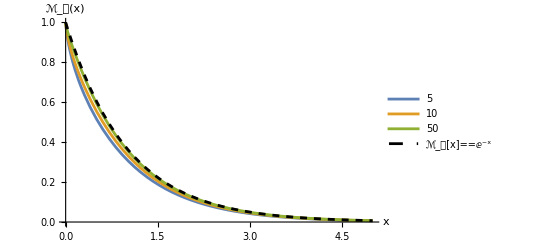

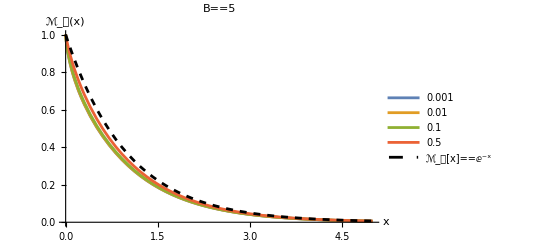

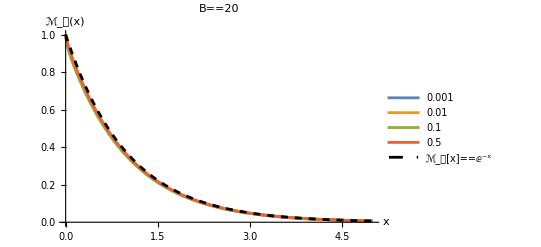

```mathematica
ℳ𝓂=P𝓂/.X->ⅇ^(z B)-1;
Bs={5,10,50};
Show[Plot[Evaluate[ℳ𝓂/.X->ⅇ^(z B)/.c->0.1/.B->Bs],{z,0,5},PlotRange->{0,1},PlotLegends->LineLegend[Bs,LegendLabel->"burst size B"],AxesLabel->{x,Subscript[ℳ, 𝓂][x]}],
Plot[ⅇ^-z,{z,0,5},PlotRange->{0,1},PlotStyle->{{Dashed,Black}},PlotLegends->{Subscript[ℳ, 𝓂][x]==ⅇ^-x}]]
cs={0.001,0.01,0.1,0.5};
Show[Plot[Evaluate[ℳ𝓂/.X->ⅇ^(z B)/.c->cs/.B->5],{z,0,5},PlotRange->{0,1},PlotLegends->LineLegend[cs,LegendLabel->"cost c"],AxesLabel->{x,Subscript[ℳ, 𝓂][x]},PlotLabel->B==5],
Plot[ⅇ^-z,{z,0,5},PlotRange->{0,1},PlotStyle->{{Dashed,Black}},PlotLegends->{Subscript[ℳ, 𝓂][x]==ⅇ^-x}]]
Show[Plot[Evaluate[ℳ𝓂/.X->ⅇ^(z B)/.c->cs/.B->20],{z,0,5},PlotRange->{0,1},PlotLegends->LineLegend[cs,LegendLabel->"cost c"],AxesLabel->{x,Subscript[ℳ, 𝓂][x]},PlotLabel->B==20],
Plot[ⅇ^-z,{z,0,5},PlotRange->{0,1},PlotStyle->{{Dashed,Black}},PlotLegends->{Subscript[ℳ, 𝓂][x]==ⅇ^-x}]]
```

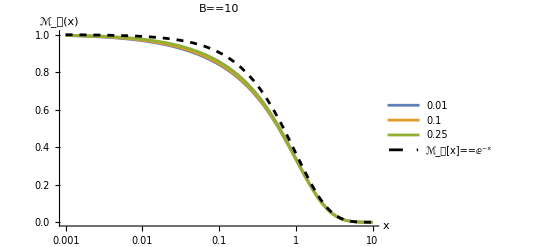

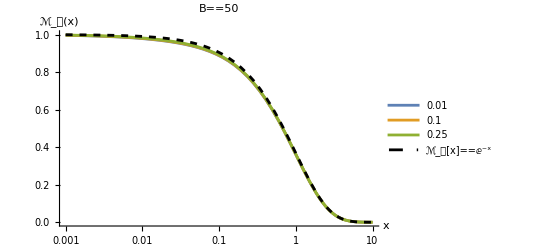

```mathematica
cs={0.01,0.1,0.25};
Show[LogLinearPlot[Evaluate[ℳ𝓂/.X->ⅇ^(z B)/.c->cs/.B->10],{z,0.001,10},PlotRange->{0,1},PlotLegends->LineLegend[cs,LegendLabel->"cost c"],AxesLabel->{x,Subscript[ℳ, 𝓂][x]},PlotLabel->B==10],
LogLinearPlot[ⅇ^-z,{z,0.001,10},PlotRange->{0,1},PlotStyle->{{Dashed,Black}},PlotLegends->{Subscript[ℳ, 𝓂][x]==ⅇ^-x}]]
Show[LogLinearPlot[Evaluate[ℳ𝓂/.X->ⅇ^(z B)/.c->cs/.B->50],{z,0.001,10},PlotRange->{0,1},PlotLegends->LineLegend[cs,LegendLabel->"cost c"],AxesLabel->{x,Subscript[ℳ, 𝓂][x]},PlotLabel->B==50],
LogLinearPlot[ⅇ^-z,{z,0.001,10},PlotRange->{0,1},PlotStyle->{{Dashed,Black}},PlotLegends->{Subscript[ℳ, 𝓂][x]==ⅇ^-x}]]
```

#### retrieving Lea and Coulson when B = 1 (binary fission)

for bacteria B=1 (burst size  = 2) and no cost (c=0) the model becomes Lea and Coulson's
the PGF becomes :P_𝓂[z](->)_(B->1
c->0)1-X Log[1+1/X]  with X=1/z^B-1=1/z-1
the series coefficients at z=0 give the probailities of 𝓂=k: ℙ[𝓂=k|𝓂>0]=1/(k+k^2)
the classic Lea & Coulson result

```mathematica
(B X^(-1/B) Hypergeometric2F1[1/B,1/B+1/(1-c),1/B+(-2+c)/(-1+c),-1/X])/(1+B-c)/.B->1/.c->0//fs
%/.X->1/z-1//fs
SeriesCoefficient[%,{z,0,k}]
```

1-X Log[1+1/X]

1+((-1+z) Log[1/(1-z)])/z

Piecewise[{{0, k==0}, {1/(k+k^2), k≥1}, {0, True}}]

### Probability of successful infection

#### Explicit formula

ℙ[OverBar[EST]]=1-Θ[r](1-ⅇ^(-2 q r))
ℙ[OverBar[SV]]=ℳ_𝓂[ν q_k]
ℙ[OverBar[DN]|OverBar[EST]]=ⅇ^(-q Abs[r](√(1+2 ν/r^2)-1))
we can check (by taking either r>0 or r<0 or |r| -> 0) that we have

Probability of successful infection: 
ℙ[INF]=1-ℙ[OverBar[INF]]=1-Exp[-q(r+√(2ν+1)+√(2ν+r^2)-1)]

```mathematica
probas={ℙ[OverBar[EST]]->1-Θ[r](1-ⅇ^(-2 q r)),ℙ[OverBar[SV]]->Subscript[ℳ, 𝓂][ν q],Subscript[ℳ, 𝓂]->Function[x,(1+x)/(1+2x)ⅇ^-x],ℙ[OverBar[DN],OverBar[EST]]->Exp[-(√(r^2+2 ν)-Abs[r]) q]};
conds=ν>0&&q>0;
(*fs[ⅇ^(-q (r+√(r^2+2 ν)))==ℙ[OverBar[EST]]ℙ[OverBar[DN],OverBar[EST]]/.probas,conds&&#]&/@{r>0,r<0}*)
Pinfcalc=fs[1-ℙ[OverBar[EST]]ℙ[OverBar[SV]]ℙ[OverBar[DN],OverBar[EST]]/.probas,conds];
Pinf=1-(1+ν q)/(1+2ν q)ⅇ^(-ν q)ⅇ^(-q (r+√(r^2+2 ν)));
PinfLow=1-ⅇ^(-ν q)ⅇ^(-q (r+√(r^2+2 ν)));
fs[Pinfcalc==Pinf/.probas,conds&&#]&/@{r>0,r<0}
```

{True,True}

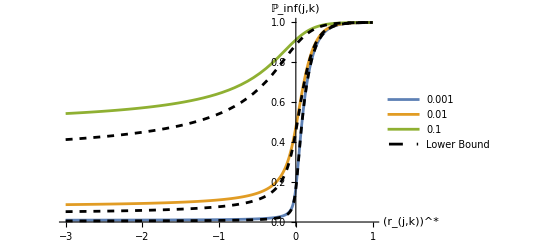

```mathematica
νs={0.001,0.01,0.1};
Show[Plot[Evaluate[Pinf/.ν->νs/.q->4],{r,-3,1},PlotRange->{0,1},AxesLabel->{SuperStar[Subscript[r, j,k]],Subscript[ℙ, inf][j,k]},PlotLegends->LineLegend[νs,LegendLabel->ν]],
Plot[Evaluate[PinfLow/.ν->νs/.q->4],{r,-3,1},PlotRange->{0,1},PlotStyle->{{Dashed,Black}},PlotLegends->LineLegend[{"Lower Bound"}]]]
```

```mathematica
Log[1-ℙ[OverBar[EST]]ℙ[OverBar[DN],OverBar[EST]]]//.probas/.ν->0.01/.q->4/.r->-1
Log[1-ℙ[OverBar[SV]]]//.probas/.ν->0.01/.q->4/.r->-1
Log[1-ℙ[OverBar[EST]]]//.probas/.ν->0.01/.q->4/.r->0.2//N
```

-3.24367

-2.593

-0.225517

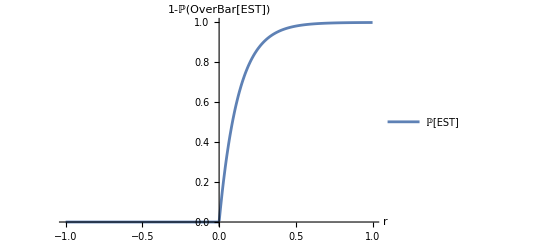

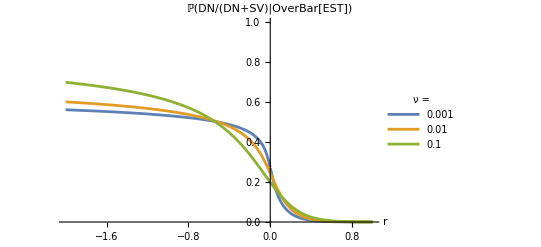

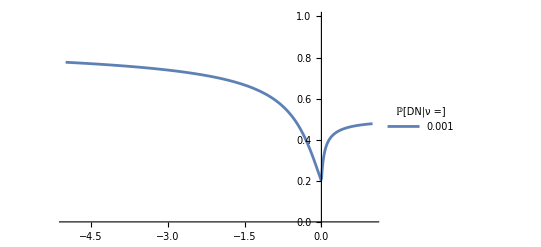

```mathematica
Plot[Evaluate[1-ℙ[OverBar[EST]]/.probas/.ν->νs/.q->4],{r,-1,1},PlotRange->{0,1},PlotLegends->LineLegend[{"ℙ[EST]"}],AxesLabel->{r,1-ℙ[OverBar[EST]]}]
Plot[Evaluate[Log[1-ℙ[OverBar[EST]]ℙ[OverBar[DN],OverBar[EST]]]/(Log[1-ℙ[OverBar[EST]]ℙ[OverBar[DN],OverBar[EST]]]+Log[1-ℙ[OverBar[SV]]])//.probas/.ν->νs/.q->4],{r,-2,1},PlotRange->{0,1},PlotLegends->LineLegend[νs,LegendLabel->"ν = "],AxesLabel->{r,ℙ[DN/(DN+SV)|OverBar[EST]]}]
Plot[Evaluate[Log[(1-ℙ[OverBar[EST]]ℙ[OverBar[DN],OverBar[EST]])ℙ[OverBar[EST]]]/(Log[(1-ℙ[OverBar[EST]]ℙ[OverBar[DN],OverBar[EST]])ℙ[OverBar[EST]]]+Log[(1-ℙ[OverBar[SV]])ℙ[OverBar[EST]]])//.probas/.ν->0.1/.q->4],{r,-5,1},PlotRange->{0,1},PlotLegends->LineLegend[νs,LegendLabel->"ℙ[DN|ν =] "]]
```

```mathematica
Pinfcalc=fs[1-ℙ[OverBar[EST]]ℙ[OverBar[SV]]ℙ[OverBar[DN],OverBar[EST]]/.probas,conds];
Pinf=1-Exp[-q(r+ν(*√(2ν+1)-1*)+√(2ν+r^2))];
fs[Pinf==Pinfcalc,conds&&#]&/@{r>0,r<0}
fs[{1,1}==Limit[Pinf/Pinfcalc,r->0,Direction->#,Assumptions->conds],conds]&/@{"FromAbove","FromBelow"}
Plot[Evaluate[Pinf/.ν->0.01/.α->{1,Log[100]}/.q->3],{r,-1,1},PlotRange->{0,1},AxesLabel->{SuperStar[Subscript[r, j,k]],Subscript[ℙ, inf][j,k]}]
```

{True,True}

{True,True}

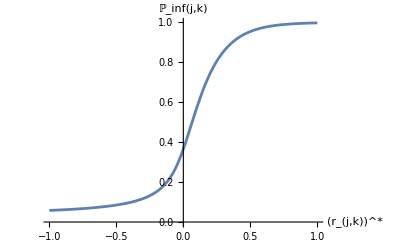

```mathematica
probas={ℙ[OverBar[EST]]->1-Θ[r](1-ⅇ^(-2 q r)),ℙ[OverBar[SV]]->ⅇ^(-q ν)(*ⅇ^(-q (√(1+2 ν)-1))*),ℙ[OverBar[DN],OverBar[EST]]->ⅇ^(-q Abs[r](√(1+2 ν/r^2)-1))};
conds=ν>0&&q>0;
Pinfcalc=fs[1-ℙ[OverBar[EST]]ℙ[OverBar[SV]]ℙ[OverBar[DN],OverBar[EST]]/.probas,conds];
Pinf=1-Exp[-q(r+ν(*√(2ν+1)-1*)+√(2ν+r^2))];
fs[Pinf==Pinfcalc,conds&&#]&/@{r>0,r<0}
fs[{1,1}==Limit[Pinf/Pinfcalc,r->0,Direction->#,Assumptions->conds],conds]&/@{"FromAbove","FromBelow"}
Plot[Evaluate[Pinf/.ν->0.01/.α->{1,Log[100]}/.q->3],{r,-1,1},PlotRange->{0,1},AxesLabel->{SuperStar[Subscript[r, j,k]],Subscript[ℙ, inf][j,k]}]
```

#### consistency with previous results in the limit

we retrieve our former formulas if we assume ν<<1
for ER from subcriticals: 1-ⅇ^(-q ν(1-1/r)) 
for establishment of supercritical:1-ⅇ^(-2 q r) 
where q=q_k, ν=2U Π[j,k] and r=r_(j,k)^*

```mathematica
fs[1-ⅇ^(-q ν(1-1/r))==1-Exp[nls[Log[1-Pinf],{ν,0,1}]],r<0]
fs[1-ⅇ^(-2 q r)==1-Exp[nls[Log[1-Pinf],{ν,0,0}]],r>0]
```

True

True

### Laplace approx as in Anciaux et al 2018

#### pdf of mutant growth rates

-Graphics-

r'=1-1/R_k^2 χ_n^2[d_(j,k)^2]
rewrite: {d_(j,k)->√(2δ ρ),R_k->√(2ρ),n->2θ}
r'=1-(χ_(2 θ)^2[2 δ ρ])/(2 ρ)

```mathematica
repar={Subscript[d, j,k]->√(2δ ρ),Subscript[R, k]->√(2ρ),n->2θ};
conds=y<1&&ρ>0&&θ>=1/2&&δ>1;
(1-1/Subscript[R, k]^2(Subscript[χ, n]^2)[Subscript[d, j,k]^2])/.repar
```

1-(χ_(2 θ)^2[2 δ ρ])/(2 ρ)

pdf : f[y]=ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]
with ψ=Hypergeometric0F1Regularized

```mathematica
fs[ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]==Expectation[DiracDelta[y-(1-1/Subscript[R, k]^2(Subscript[χ, n]^2)[Subscript[d, j,k]^2])],(Subscript[χ, n]^2)[Subscript[d, j,k]^2]\[Distributed]NoncentralChiSquareDistribution[n,Subscript[d, j,k]^2],Assumptions->conds]/.repar/.ψ->Hypergeometric0F1Regularized,conds]
```

True

-Graphics-

approx  of  hypergeometric:ψ[θ,h]≈_(h>>1, δ!=0) (h^(1/4-θ/2)ⅇ^(2 √h))/(2 √π)

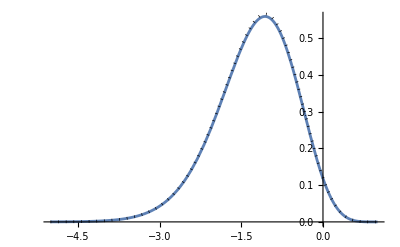

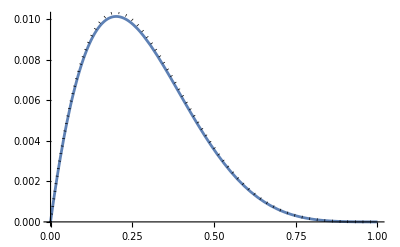

```mathematica
pars={R->4,ρ->R^2/2,δ->2,θ->2,ψ->Hypergeometric0F1Regularized};
Show[Plot[ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pars,{y,-5,1}],Plot[ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]/.ψ->Function[{θ,h},(h^(1/4-θ/2)ⅇ^(2 √h))/(2 √π)]//.pars,{y,-5,1},PlotStyle->{{Dotted,Black}}]]
Show[Plot[y Θ[y] ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pars,{y,0,1}],
Plot[y Θ[y] ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]/.ψ->Function[{θ,h},(h^(1/4-θ/2)ⅇ^(2 √h))/(2 √π)]//.pars,{y,0,1},PlotStyle->{{Dotted,Black}}]]
```

𝒻_y[y]≈_(ρ>>1)(δ^(1/4-θ/2) √ρ)/(2 √π)ⅇ^(-ρ(1-y+δ-2 √(δ(1-y))))(1-y)^(θ/2-3/4)

```mathematica
fs[(δ^(1/4-θ/2) √ρ)/(2 √π)ⅇ^(-ρ(1-y+δ-2 √(δ(1-y))))(1-y)^(θ/2-3/4)==(*(ⅇ^(-ρ(1-y+δ-2 √(δ-y δ)) ρ) (1-y)^(θ/2-3/4) δ^(1/4-θ/2) √ρ)/(2 √π)==*)ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]/.ψ->Function[{θ,h},(h^(1/4-θ/2)ⅇ^(2 √h))/(2 √π)]//po,conds]
```

True

integral in native variables using the approx for the HGF_(0,1) function
Π[i,k]≈_(ρ>>1)∫_0^1 y 𝒻_Y[y]ⅆy

change variables in the integral: 
y->x=X[y]=2(1-√(1-y))  so that x=Y[x]=x(1-x/4)

```mathematica
x(1-x/4)==y/.ft[Solve[2(1-√(1-y))==x,y]]//fs
y2x={X->Function[y,2(1-√(1-y))],Y->Function[x,x(1-x/4)]};
{Y[x],X[y]}/.y2x
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

True

{(1-x/4) x,2 (1-√(1-y))}

introduce the WT decay rate : rD=|r[O_j,k]|=-(1-1/R_k^2 d_(j,k)^2)=δ-1
introduce xD=-Y[-rD]=2(√(1+rD)-1)
we have reparameterization: δ=1/4 (2+xD)^2  or xD=2 (√δ-1)

```mathematica
rD->-(1-1/Subscript[R, k]^2 Subscript[d, j,k]^2)//.repar
fs[δ/.ft[Solve[xD==2(√(1+rD)-1)/.%,δ]],xD>0]
2(√(1+rD)-1)/.rD->δ-1
```

rD→-1+δ

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

1/4 (2+xD)^2

2 (-1+√δ)

ⅆy=ⅆY[x]=Y'[x]ⅆx
Π[i,k]=∫_0^1 y 𝒻_Y[y]ⅆy=∫_0^2 Y[x] 𝒻_Y[Y[x]]Y'[x]ⅆx=K∫_0^2 ⅇ^(-1/4 (x+xD)^2 ρ) (1-x/4) x (1-x/2)^(θ-1/2)ⅆx
K=((1+xD/2)^(1/2-θ)√ρ)/(2 √π)
we cannot evaluate this integral exactly

```mathematica
y2x={X->Function[y,2(1-√(1-y))],Y->Function[x,x(1-x/4)],δ->1/4 (2+xD)^2};
{X[0],X[1]}/.y2x
IntegrandX=((1+xD/2)^(1/2-θ)√ρ)/(2 √π)ⅇ^(-1/4 (x+xD)^2 ρ) (1-x/4) x (1-x/2)^(θ-1/2);
fs[1==(Y[x] 𝒻[Y[x]]Y'[x]/.y2x)/IntegrandX//po,ρ>0&&0<=x<2&&xD>0]
```

{0,2}

(1-x/2)^θ √((2+xD) ρ)==ⅇ^(1/4 (x+xD)^2 ρ) √π (2-x)^(3/2) (1+xD/2)^θ 𝒻[(1-x/4) x]

#### Laplace approximation

the integral is :
Π[i,k]=K∫_0^2 ⅇ^(-1/4 (x+xD)^2 ρ) h[x]ⅆx
where h[x]=(1-x/4) x (2-x)^(θ-1/2)
it is dominated by the value near the maximum of the exponential term ⅇ^(-1/4 (x+xD)^2 ρ)  on [0,2] which is at x=0
to leading (zeroth) order :h[x]=x(1+o[1])
to the first order:h[x]=ⅇ^(-(x θ)/2) x(1+o[x])
to the second order:h[x]=ⅇ^(1/32 x (x-4 (4+x) θ)) x
the first order is clearly more accurate than the zeroth order for mild ρ
there is not much gain by the second order

{x,ⅇ^(-(x θ)/2) x,ⅇ^(1/32 x (x-4 (4+x) θ)) x}

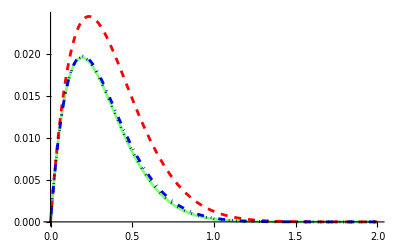

```mathematica
(Exp[nls[Log[(1-x/4) x (1-x/2)^(θ-1/2)],{x,0,#}]]//po//fs)&/@{0,1,2}
Plot[Evaluate[ft[{x(1-x/4)ⅇ^(-1/4 ρ(x+xD)^2)(1-x/2)^(θ-1/2),%ⅇ^(-1/4 (x+xD)^2 ρ)}]/.xD->2(√(1+rD)-1)/.rD->δ-1//.pars],{x,0,2},PlotStyle->{{Opacity[0.5],Green},{Dashed,Red},{Blue,DotDashed},{Dotted,Black}}]
```

compared  to  the  exact  integrand, the first order is still better than the zeroth order

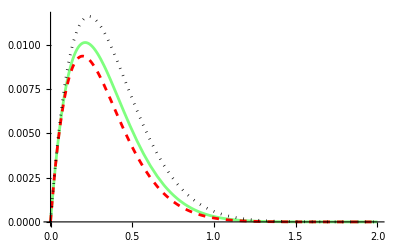

```mathematica
Plot[Evaluate[{y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]/.y->Y[x]/.y2x,K x ⅇ^(-(x θ)/2)ⅇ^(-1/4 (x+xD)^2 ρ),K x ⅇ^(-1/4 (x+xD)^2 ρ)}/.K->((1+xD/2)^(1/2-θ)√ρ)/(2 √π)/.xD->2(√δ-1)//.pars],{x,0,2},PlotStyle->{{Green,Opacity[0.5]},{Dashed,Red},{Dotted,Black}}]
```

we approximate:h[x]≈ⅇ^(-(x θ)/2) x to get an explicit approximate expression:
Π[i,k]=K∫_0^2 ⅇ^(-1/4 (x+xD)^2 ρ) h[x]ⅆx≈K∫_0^∞ ⅇ^(-1/4 (x+xD)^2 ρ) ⅇ^(-(x θ)/2) x ⅆx=(ⅇ^(-(xD^2 ρ)/4) (1+xD/2)^(1/2-θ) (2 √ρ-ⅇ^((θ+xD ρ)^2/(4 ρ)) √π (θ+xD ρ) Erfc[(θ+xD ρ)/(2 √ρ)]))/(2 √π ρ)

```mathematica
I0=fs[K∫_0^∞ ⅇ^(-1/4 (x+xD)^2 ρ) x ⅆx/.K->((1+xD/2)^(1/2-θ)√ρ)/(2 √π)//po,ρ>0&&xD>0&&θ>=1/2] (*zeroth order h[x]≈ x*)
I1=fs[K∫_0^∞ ⅇ^(-1/4 (x+xD)^2 ρ) ⅇ^(-(x θ)/2) x ⅆx/.K->((1+xD/2)^(1/2-θ)√ρ)/(2 √π)//po,ρ>0&&xD>0&&θ>=1/2](*first order h[x]≈ⅇ^(-(x θ)/2) x*)
```

2^(-3/2+θ) (2+xD)^(1/2-θ) ((2 ⅇ^(-(xD^2 ρ)/4))/(√π √ρ)-xD Erfc[(xD √ρ)/2])

(ⅇ^(-(xD^2 ρ)/4) (1+xD/2)^(1/2-θ) (2 √ρ-ⅇ^((θ+xD ρ)^2/(4 ρ)) √π (θ+xD ρ) Erfc[(θ+xD ρ)/(2 √ρ)]))/(2 √π ρ)

we can express it back in terms of the native parameters:{xD→2 (-1+√δ),δ→(d_(j,k)^2)/R_k^2,ρ→R_k^2/2,θ→n/2}
we have : ⅇ^(-(xD^2 ρ)/4) (1+xD/2)^(1/2-θ)=ⅇ^(-1/2 (d_(j,k)-R_k)^2) (R_k/(d_(j,k)))^((n-1)/2)
and , introducing:y=y_(j,k)=(θ+xD ρ)/(√(2ρ))=d_(j,k)+n/(2 R_k)-R_k:
Π[i,k]=1/R_k ⅇ^(-1/2 (d_(j,k)-R_k)^2) (R_k/(d_(j,k)))^((n-1)/2)(√(2/π)-ⅇ^(y^2/2) y Erfc[y/(√2)])

```mathematica
unpar=ft[{xD->2(√δ-1),Solve[{Subscript[d, j,k]==√(2δ ρ),Subscript[R, k]==√(2ρ),n/2==θ},{δ,ρ,θ}]}]
fs[ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)==ⅇ^(-(xD^2 ρ)/4) (1+xD/2)^(1/2-θ) //.unpar,Subscript[d, j,k]>0&&Subscript[R, k]>0&&n>=1]
fs[{I1/(ⅇ^(-(xD^2 ρ)/4) (1+xD/2)^(1/2-θ))/.ft[Solve[(θ+xD ρ)/(√(2ρ))==y,θ]],(θ+xD ρ)/(√(2ρ))}//.unpar,Subscript[d, j,k]>0&&Subscript[R, k]>0&&n>=1]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{xD→2 (-1+√δ),δ→(d_(j,k)^2)/R_k^2,ρ→R_k^2/2,θ→n/2}

True

{(√(2/π)-ⅇ^(y^2/2) y Erfc[y/(√2)])/R_k,n/(2 R_k)-R_k+d_(j,k)}

in terms of the original parmeters
Π[i,k]≈ 1/R_k ⅇ^(-1/2 (d_(j,k)-R_k)^2) (R_k/(d_(j,k)))^((n-1)/2)(√(2/π)-ⅇ^((y_(j,k)^2)/2) y_(j,k) Erfc[(y_(j,k))/(√2)]) where y_(j,k)=d_(j,k)-R_k+n/(2 R_k)

```mathematica
finalExpression1= 1/Subscript[R, k] ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)(√(2/π)-ⅇ^(Subscript[y, j,k]^2/2) Subscript[y, j,k] Erfc[Subscript[y, j,k]/(√2)])/.Subscript[y, j,k]->Subscript[d, j,k]+n/(2 Subscript[R, k])-Subscript[R, k];
fs[1==I1/finalExpression1//.unpar,Subscript[d, j,k]>0&&Subscript[R, k]>0&&n>=1]
```

True

The zeroth order is just the same but ignoring n/(2 R_k)<<d_(j,k)-R_k in the expression for y_(j,k)
no gain in simplicity and less accurate

```mathematica
finalExpression0= 1/Subscript[R, k] ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)(√(2/π)-ⅇ^(Subscript[y, j,k]^2/2) Subscript[y, j,k] Erfc[Subscript[y, j,k]/(√2)])/.Subscript[y, j,k]->Subscript[d, j,k]-Subscript[R, k];
fs[1==I0/finalExpression0//.unpar,Subscript[d, j,k]>0&&Subscript[R, k]>0&&n>=1]
```

True

### Matching moment gaussian approx

#### gaussian approx on the bulk

CGF of the exact r:C_r[z]=log 𝔼[ⅇ^(r z)]=z (1-δ ρ/(ρ+z))+θ Log[ρ/(ρ+z)]
with  :{δ→(d_(j,k)^2)/R_k^2,ρ→R_k^2/2,θ→n/2}

```mathematica
pareq={Subscript[d, j,k]==√(2δ ρ),Subscript[R, k]==√(2 ρ),n/2==θ};
repar=ft [Solve[pareq,{Subscript[d, j,k],Subscript[R, k],n}]];
unpar=ft[Solve[pareq,{δ,ρ,θ}]]
conds=y<1&&ρ>0&&θ>=1/2&&δ>1&&ϵ>0;
Expectation[ⅇ^(z (1-1/Subscript[R, k]^2(Subscript[χ, n]^2)[Subscript[d, j,k]^2])),(Subscript[χ, n]^2)[Subscript[d, j,k]^2]\[Distributed]NoncentralChiSquareDistribution[n,Subscript[d, j,k]^2],Assumptions->conds];
Cr=Function[z,z (1-δ ρ/(ρ+z))+θ Log[ρ/(ρ+z)]];
fs[Cr[z]==Log[%%]/.repar//po,conds]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{δ→(d_(j,k)^2)/R_k^2,ρ→R_k^2/2,θ→n/2}

True

let 
μ=𝔼[r]=1-(δ+θ) λ
σ=√𝕍[r]=√(2 δ+θ) λ
we would like to see when we have r∝𝒩[μ,σ^2]
this amounts to show that ρ=(r-μ)/σ∝𝒩[0,1]
the CGF of ρ is:C_ρ[z]=Log [𝔼[ⅇ^((r-μ)/σ z)]]=C_r[z/σ]-μ/σ z=(z (z+η (2+z η) θ))/(2+2 z η)-θ Log[1+z η]
where η=1/(√(2 δ ρ+θ))
As η->0 (as n and δ increase)
we get : C_ρ[z]=z^2/2(1-z η+o[η])
showing that the distribution converges to a standard 𝒩[0,1] (with CGF z^2/2) for its bulk (below z=O[1/η])

```mathematica
moments=Thread[{μ,σ}->fs[{Cr'[0],√Cr''[0]}//po,conds]]
fs[Cr[z/σ]-μ/σ z/.moments/.ft[Solve[1/(√(2 δ ρ+θ))==η,δ]]//po,conds&&η>0]
nls[%/(z^2/2),{η,0,1}]
```

{μ→1-δ-θ/ρ,σ→(√(θ+2 δ ρ))/ρ}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(z (z+η (2+z η) θ))/(2+2 z η)-θ Log[1+z η]

1-z η

#### Computation of Π[j, k]

matching moment gaussian: r'~N[μ,σ]⇒Π[j,k]=1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])

```mathematica
Expectation[r Θ[r],r\[Distributed]NormalDistribution[μ,σ]]
```

1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])

moments from the exact distribution: μ=1-(d_(j,k)^2+n)/R_k^2 and σ=√((2 n+4 d_(j,k)^2)/R_k^4)

```mathematica
fs[{δ,σ^2}/.moments/.unpar,conds]
```

{(d_(j,k)^2)/2,(2 (n+2 d_(j,k)^2))/R_k^4}

```mathematica
fs[1-(Subscript[d, j,k]^2+n)/Subscript[R, k]^2==Expectation[(1-1/Subscript[R, k]^2(Subscript[χ, n]^2)[Subscript[d, j,k]^2]),(Subscript[χ, n]^2)[Subscript[d, j,k]^2]\[Distributed]NoncentralChiSquareDistribution[n,Subscript[d, j,k]^2],Assumptions->conds],conds]
fs[(2 n+4 Subscript[d, j,k]^2)/Subscript[R, k]^4==Expectation[(1-1/Subscript[R, k]^2(Subscript[χ, n]^2)[Subscript[d, j,k]^2])^2-(1-(Subscript[d, j,k]^2+n)/Subscript[R, k]^2)^2,(Subscript[χ, n]^2)[Subscript[d, j,k]^2]\[Distributed]NoncentralChiSquareDistribution[n,Subscript[d, j,k]^2],Assumptions->conds],conds]
```

True

True

-Graphics-

### numerical checks

```mathematica
pp={R->4.5,ρ->R^2/2,xD->2(√δ-1),δ->d^2/R^2,θ->n/2,n->2,ψ->Hypergeometric0F1Regularized}&;
dmin=0;dmax=7.5;rge={10^-4,1};
Show[ListLogPlot[Table[{d,NIntegrate[y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pp[d],{y,0,1}]},{d,dmin,dmax,0.2}],PlotStyle->{Darker[Orange]},PlotRange->{All,rge},AxesLabel->{Subscript[d, j,k],Π[j,k]},PlotLegends->LineLegend[{"exact"}]],LogPlot[Min[{((√2)/(√π Subscript[R, k])+ ⅇ^((n/(2 Subscript[R, k])+ Subscript[d, j,k]-Subscript[R, k])^2/2) Erfc[1/(√2)(n/(2 Subscript[R, k])+Subscript[d, j,k]-Subscript[R, k])] (1-Subscript[d, j,k]/Subscript[R, k]-n/(2 Subscript[R, k]^2))) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2),1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])/.{ μ->1-(Subscript[d, j,k]^2+n)/Subscript[R, k]^2 , σ->√((2 n+4 Subscript[d, j,k]^2)/Subscript[R, k]^4)}}]/.Subscript[R, k]->R//.pp[Subscript[d, j,k]],{Subscript[d, j,k],dmin,dmax},PlotStyle->{{Blue,Opacity[0.5]}},PlotLegends->LineLegend[{"Min[Laplace,Gaussian]","Matching moment Gaussian Approx"}]],LogPlot[Θ[d-R]//.pp[1],{d,dmin,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->Green,PlotLegends->LineLegend[{"ER domain"}]]]
```

-Graphics-

```mathematica
pp={R->3,ρ->R^2/2,xD->2(√δ-1),δ->d^2/R^2,θ->n/2,n->3,ψ->Hypergeometric0F1Regularized}&;
dmin=0;dmax=6;rge={10^-4,1};
Show[ListLogPlot[Table[{d,NIntegrate[y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pp[d],{y,0,1}]},{d,dmin,dmax,0.2}],PlotStyle->{Darker[Orange]},PlotRange->{All,rge},AxesLabel->{Subscript[d, j,k],Π[j,k]},PlotLegends->LineLegend[{"exact"}]],LogPlot[Min[{((√2)/(√π Subscript[R, k])+ ⅇ^((n/(2 Subscript[R, k])+ Subscript[d, j,k]-Subscript[R, k])^2/2) Erfc[1/(√2)(n/(2 Subscript[R, k])+Subscript[d, j,k]-Subscript[R, k])] (1-Subscript[d, j,k]/Subscript[R, k]-n/(2 Subscript[R, k]^2))) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2),1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])/.{ μ->1-(Subscript[d, j,k]^2+n)/Subscript[R, k]^2 , σ->√((2 n+4 Subscript[d, j,k]^2)/Subscript[R, k]^4)}}]/.Subscript[R, k]->R//.pp[Subscript[d, j,k]],{Subscript[d, j,k],dmin,dmax},PlotStyle->{{Blue,Opacity[0.5]}},PlotLegends->LineLegend[{"Min[Laplace,Gaussian]","Matching moment Gaussian Approx"}]],LogPlot[Θ[d-R]//.pp[1],{d,dmin,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->Green,PlotLegends->LineLegend[{"ER domain"}]]]
```

-Graphics-

```mathematica
pp={R->1.5,ρ->R^2/2,xD->2(√δ-1),δ->d^2/R^2,θ->n/2,n->2,ψ->Hypergeometric0F1Regularized}&;
dmin=0.1R//.pp[1];dmax=5;rge={10^-4,1};
Show[ListLogPlot[Table[{d,NIntegrate[y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pp[d],{y,0,1}]},{d,dmin,dmax,0.2}],PlotStyle->{Darker[Orange]},PlotRange->{All,rge},AxesLabel->{Subscript[d, j,k],Π[j,k]},PlotLegends->LineLegend[{"exact"}]],LogPlot[Min[{((√2)/(√π Subscript[R, k])+ ⅇ^((n/(2 Subscript[R, k])+ Subscript[d, j,k]-Subscript[R, k])^2/2) Erfc[1/(√2)(n/(2 Subscript[R, k])+Subscript[d, j,k]-Subscript[R, k])] (1-Subscript[d, j,k]/Subscript[R, k]-n/(2 Subscript[R, k]^2))) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2),1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])/.{ μ->1-(Subscript[d, j,k]^2+n)/Subscript[R, k]^2 , σ->√((2 n+4 Subscript[d, j,k]^2)/Subscript[R, k]^4)}}]/.Subscript[R, k]->R//.pp[Subscript[d, j,k]],{Subscript[d, j,k],dmin,dmax},PlotStyle->{{Blue,Opacity[0.5]}},PlotLegends->LineLegend[{"Min[Laplace,Gaussian]","Matching moment Gaussian Approx"}]],LogPlot[Θ[d-R]//.pp[1],{d,dmin,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->Green,PlotLegends->LineLegend[{"ER domain"}]]]
```

-Graphics-

```mathematica
pp={R->1.5,ρ->R^2/2,xD->2(√δ-1),δ->d^2/R^2,θ->n/2,n->3,ψ->Hypergeometric0F1Regularized}&;
dmin=0;dmax=4.5;rge={10^-4,1};
Show[ListLogPlot[Table[{d,NIntegrate[y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pp[d],{y,0,1}]},{d,dmin,dmax,0.2}],PlotStyle->{Darker[Orange]},PlotRange->{All,rge},AxesLabel->{Subscript[d, j,k],Π[j,k]},PlotLegends->LineLegend[{"exact"}]],LogPlot[Min[{((√2)/(√π Subscript[R, k])+ ⅇ^((n/(2 Subscript[R, k])+ Subscript[d, j,k]-Subscript[R, k])^2/2) Erfc[1/(√2)(n/(2 Subscript[R, k])+Subscript[d, j,k]-Subscript[R, k])] (1-Subscript[d, j,k]/Subscript[R, k]-n/(2 Subscript[R, k]^2))) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2),1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])/.{ μ->1-(Subscript[d, j,k]^2+n)/Subscript[R, k]^2 , σ->√((2 n+4 Subscript[d, j,k]^2)/Subscript[R, k]^4)}}]/.Subscript[R, k]->R//.pp[Subscript[d, j,k]],{Subscript[d, j,k],dmin,dmax},PlotStyle->{{Blue,Opacity[0.5]}},PlotLegends->LineLegend[{"Min[Laplace,Gaussian]","Matching moment Gaussian Approx"}]],LogPlot[Θ[d-R]//.pp[1],{d,dmin,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->Green,PlotLegends->LineLegend[{"ER domain"}]]]
```

-Graphics-

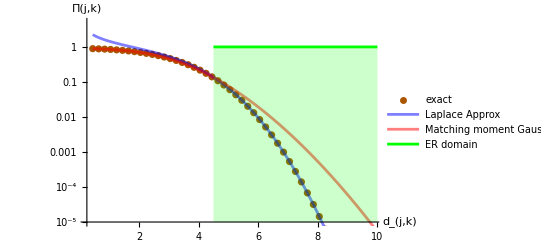

```mathematica
pp={R->4.5,ρ->R^2/2,xD->2(√δ-1),δ->d^2/R^2,θ->n/2,n->2,ψ->Hypergeometric0F1Regularized}&;
dmin=0.1R//.pp[1];dmax=10;
Show[ListLogPlot[Table[{d,NIntegrate[y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pp[d],{y,0,1}]},{d,dmin,dmax,0.2}],PlotStyle->{Darker[Orange]},PlotRange->{All,{10^-5,5}},AxesLabel->{Subscript[d, j,k],Π[j,k]},PlotLegends->LineLegend[{"exact"}]],LogPlot[Evaluate[{((√2)/(√π Subscript[R, k])+ ⅇ^((n/(2 Subscript[R, k])+ Subscript[d, j,k]-Subscript[R, k])^2/2) Erfc[1/(√2)(n/(2 Subscript[R, k])+Subscript[d, j,k]-Subscript[R, k])] (1-Subscript[d, j,k]/Subscript[R, k]-n/(2 Subscript[R, k]^2))) (Subscript[R, k]/Subscript[d, j,k])^((n-1)/2)ⅇ^(-1/2 (Subscript[d, j,k]-Subscript[R, k])^2),1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])/.{ μ->1-(Subscript[d, j,k]^2+n)/Subscript[R, k]^2 , σ->√((2 n+4 Subscript[d, j,k]^2)/Subscript[R, k]^4)}}/.Subscript[R, k]->R//.pp[Subscript[d, j,k]]],{Subscript[d, j,k],dmin,dmax},PlotStyle->{{Blue,Opacity[0.5]},{Red,Opacity[0.5]}},PlotLegends->LineLegend[{"Laplace Approx","Matching moment Gaussian Approx"}]],LogPlot[Θ[d-R]//.pp[1],{d,dmin,dmax},Filling->Axis,PlotRange->{All,{10^-5,5}},PlotStyle->Green,PlotLegends->LineLegend[{"ER domain"}]]]
```

### Final profile with d_(j,k)

Aproximate expression for Π[j,k]=Π[d_(j,k)]

```mathematica
pp=.;Clear[r,ν,q];
Πexact=Function[d,NIntegrate[y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pp[d],{y,0,1}]];
ΠL=Function[d,((√2)/(√π Subscript[R, k])+ ⅇ^((n/(2 Subscript[R, k])+ d-Subscript[R, k])^2/2) Erfc[1/(√2)(n/(2 Subscript[R, k])+d-Subscript[R, k])] (1-d/Subscript[R, k]-n/(2 Subscript[R, k]^2))) (Subscript[R, k]/d)^((n-1)/2)ⅇ^(-1/2 (d-Subscript[R, k])^2)//.pp[d]];
ΠG=Function[d,1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])/.{ μ->1-(d^2+n)/Subscript[R, k]^2 , σ->√((2 n+4 d^2)/Subscript[R, k]^4)}//.pp[d]];
Πapprox=Function[d,Min[{ΠL[d],ΠG[d]}]//.pp[d]];
rr=Function[d,1-d^2/Subscript[R, k]//.pp[d]];
Pinf=1-ⅇ^(-q(r+√(2 α ν+1)+√(2ν+r^2)-1));
ℙinfapprox=Function[d,Pinf/.r->rr[d]/.ν->2U Πapprox[d]//.pp[d]];
ℙinfL=Function[d,Pinf/.r->rr[d]/.ν->2U ΠL[d]//.pp[d]];
ℙinfG=Function[d,Pinf/.r->rr[d]/.ν->2U ΠG[d]//.pp[d]];
ℙinfexact=Function[d,Pinf/.r->rr[d]/.ν->2U Πexact[d]//.pp[d]];
```

Computation  of  the  approx  is  ~ 20  times  faster on  my  computer

when q_k is large it suffices to have the Laplace approx

but when q_k is small (so that establishment is certain even if d_jk=d_jj=0) then the macthing  is better than the laplace 
(because the Gaussian is more accurate near d=0)

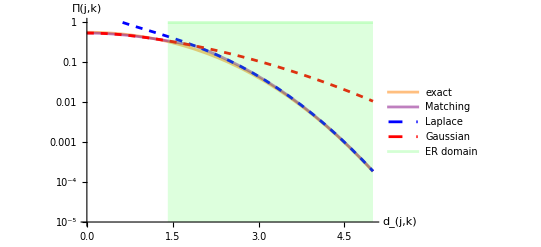

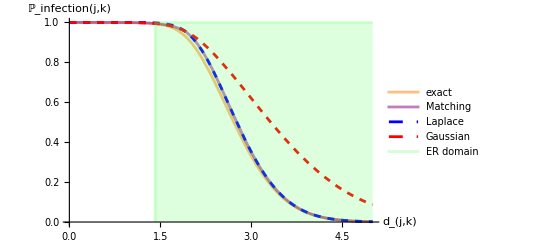

```mathematica
pp={Subscript[R, k]->2,n->2,α->1,q->2,U->2,ρ->Subscript[R, k]^2/2,xD->2(√δ-1),δ->#^2/Subscript[R, k]^2,θ->n/2,ψ->Hypergeometric0F1Regularized}&;
dmax=5;rge={10^-5,1};
Show[LogPlot[{Πexact[d],Πapprox[d],ΠL[d],ΠG[d]},{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Opacity[0.5],Orange},{Opacity[0.5],Purple},{Dashed,Blue},{Dashed,Red}},PlotRange->rge,PlotLegends->LineLegend[{"exact","Matching","Laplace","Gaussian"}],AxesLabel->{Subscript[d, j,k],Π[j,k]}],
LogPlot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]
Show[Plot[{ℙinfexact[d],ℙinfapprox[d],ℙinfL[d],ℙinfG[d]},{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Opacity[0.5],Orange},{Opacity[0.5],Purple},{Dashed,Blue},{Dashed,Red}},PlotRange->rge,PlotLegends->LineLegend[{"exact","Matching","Laplace","Gaussian"}],AxesLabel->{Subscript[d, j,k],Subscript[ℙ, infection][j,k]}],Plot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]
```

but when q_k is small (so that establishment is not certain even if d_jk=d_jj=0) 
then the macthing  is better than the laplace (because the Gaussian is more accurate near d=0)

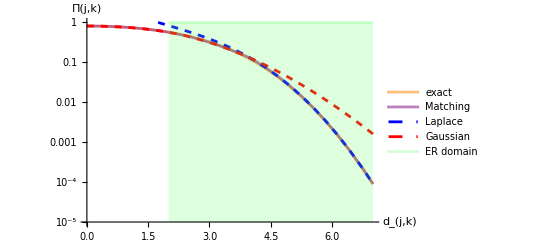

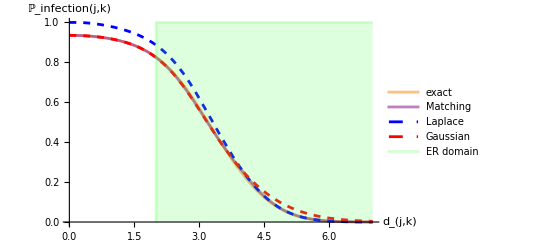

```mathematica
pp={Subscript[R, k]->4,n->3,α->1,q->0.5,U->2,ρ->Subscript[R, k]^2/2,xD->2(√δ-1),δ->#^2/Subscript[R, k]^2,θ->n/2,ψ->Hypergeometric0F1Regularized}&;
dmax=7;rge={10^-5,1};
Show[LogPlot[{Πexact[d],Πapprox[d],ΠL[d],ΠG[d]},{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Opacity[0.5],Orange},{Opacity[0.5],Purple},{Dashed,Blue},{Dashed,Red}},PlotRange->rge,PlotLegends->LineLegend[{"exact","Matching","Laplace","Gaussian"}],AxesLabel->{Subscript[d, j,k],Π[j,k]}],
LogPlot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]
Show[Plot[{ℙinfexact[d],ℙinfapprox[d],ℙinfL[d],ℙinfG[d]},{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Opacity[0.5],Orange},{Opacity[0.5],Purple},{Dashed,Blue},{Dashed,Red}},PlotRange->rge,PlotLegends->LineLegend[{"exact","Matching","Laplace","Gaussian"}],AxesLabel->{Subscript[d, j,k],Subscript[ℙ, infection][j,k]}],Plot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]
```

the maching approx seems very accurate  whenever R_k is clearly above 1 (R_k=3 q_k=0.5 here)

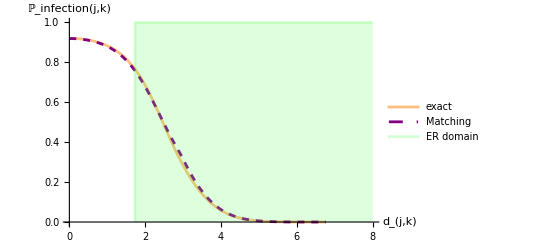

```mathematica
pp={Subscript[R, k]->3,n->3,α->1,q->0.5,U->2,ρ->Subscript[R, k]^2/2,xD->2(√δ-1),δ->#^2/Subscript[R, k]^2,θ->n/2,ψ->Hypergeometric0F1Regularized}&;
dmax=8;rge={10^-5,1};
Show[Plot[{ℙinfexact[d],ℙinfapprox[d]},{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Opacity[0.5],Orange},{Dashed,Purple}},PlotRange->rge,PlotLegends->LineLegend[{"exact","Matching","Laplace","Gaussian"}],AxesLabel->{Subscript[d, j,k],Subscript[ℙ, infection][j,k]}],Plot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]
```

When R_k is <=1  and q is small (R_k=0.9 and q_k=0.5 or 5 below) the maching approx is less accurate but still reasonable

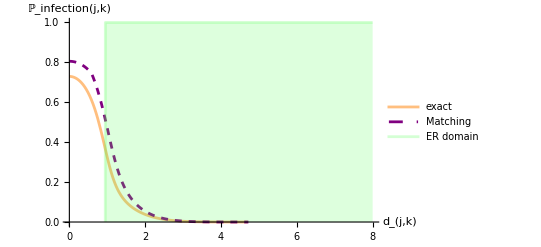

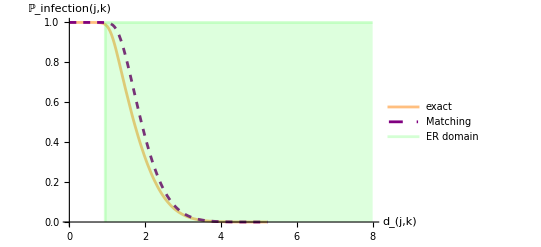

```mathematica
pp={Subscript[R, k]->0.9,n->2,α->1,q->0.5,U->1,ρ->Subscript[R, k]^2/2,xD->2(√δ-1),δ->#^2/Subscript[R, k]^2,θ->n/2,ψ->Hypergeometric0F1Regularized}&;
dmax=8;rge={10^-5,1};
Show[Plot[{ℙinfexact[d],ℙinfapprox[d]},{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Opacity[0.5],Orange},{Dashed,Purple}},PlotRange->rge,PlotLegends->LineLegend[{"exact","Matching","Laplace","Gaussian"}],AxesLabel->{Subscript[d, j,k],Subscript[ℙ, infection][j,k]}],Plot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]
pp={Subscript[R, k]->0.9,n->2,α->1,q->5,U->1,ρ->Subscript[R, k]^2/2,xD->2(√δ-1),δ->#^2/Subscript[R, k]^2,θ->n/2,ψ->Hypergeometric0F1Regularized}&;
dmax=8;rge={10^-5,1};
Show[Plot[{ℙinfexact[d],ℙinfapprox[d]},{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Opacity[0.5],Orange},{Dashed,Purple}},PlotRange->rge,PlotLegends->LineLegend[{"exact","Matching","Laplace","Gaussian"}],AxesLabel->{Subscript[d, j,k],Subscript[ℙ, infection][j,k]}],Plot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]
```

### Limited impact of α when Ν_0 is not too big

```mathematica
pp=.;Clear[r,ν,q,d,α];
Πexact=Function[d,NIntegrate[y ⅇ^(-ρ(1-y+δ)) (1-y)^(θ-1) ρ^θ ψ[θ,ρ^2(1-y) δ ]//.pp[d],{y,0,1}]];
ΠL=Function[d,((√2)/(√π Subscript[R, k])+ ⅇ^((n/(2 Subscript[R, k])+ d-Subscript[R, k])^2/2) Erfc[1/(√2)(n/(2 Subscript[R, k])+d-Subscript[R, k])] (1-d/Subscript[R, k]-n/(2 Subscript[R, k]^2))) (Subscript[R, k]/d)^((n-1)/2)ⅇ^(-1/2 (d-Subscript[R, k])^2)//.pp[d]];
ΠG=Function[d,1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)])/.{ μ->1-(d^2+n)/Subscript[R, k]^2 , σ->√((2 n+4 d^2)/Subscript[R, k]^4)}//.pp[d]];
Πapprox=Function[d,Min[{ΠL[d],ΠG[d]}]//.pp[d]];
rr=Function[d,1-d^2/Subscript[R, k]//.pp[d]];
ℙinfapprox=Function[{d,α},1-ⅇ^(-q(r+√(2 α ν+1)+√(2ν+r^2)-1))/.r->rr[d]/.ν->2U Πapprox[d]//.pp[d]];
ℙinfexact=Function[{d,α},1-ⅇ^(-q(r+√(2 α ν+1)+√(2ν+r^2)-1))/.r->rr[d]/.ν->2U Πexact[d]//.pp[d]];
```

when q_k is large it suffices to have the Laplace approx

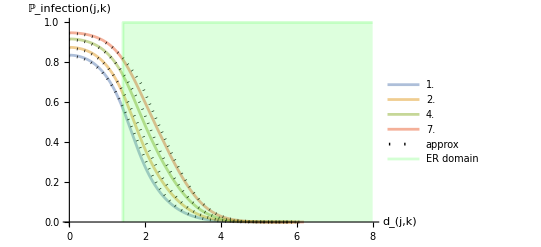

```mathematica
pp={Subscript[R, k]->2,n->2,q->0.5,U->1,ρ->Subscript[R, k]^2/2,xD->2(√δ-1),δ->#^2/Subscript[R, k]^2,θ->n/2,ψ->Hypergeometric0F1Regularized}&;
dmax=8;rge={10^-5,1};αs={1,2,4,7}//N;
Show[Plot[Evaluate[ℙinfexact[d,#]&/@αs],{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->Opacity[0.5],PlotRange->rge,PlotLegends->LineLegend[αs,LegendLabel->α],AxesLabel->{Subscript[d, j,k],Subscript[ℙ, infection][j,k]}],Plot[Evaluate[ℙinfapprox[d,#]&/@αs],{d,0,dmax},PerformanceGoal->"Speed",PlotStyle->{{Dotted,Black}},PlotRange->rge,PlotLegends->LineLegend[{"approx"}],AxesLabel->{Subscript[d, j,k],Subscript[ℙ, infection][j,k]}],Plot[Θ[-rr[d]],{d,0,dmax},Filling->Axis,PlotRange->{All,rge},PlotStyle->{{Opacity[0.25],Lighter[Green]}},PlotLegends->LineLegend[{"ER domain"}]]]//Quiet
```

### Summary of results (to update)

ℙ (infection)  by a strain j from host j (pheno x_j≈o_j)  inoculated into  target  host  k

definitions
ξ_k=r_k^max/v_k : 1/(stochastic variance in host k, in rescaled time)

q_k=Ν_0 ξ_k 

r_(j,k)^*=1-(x_j-o_k)^2/R_k^2 =(r_(j,k))/r_k^max : growth rate of parent j in host k, in rescaled time (t^*=r_k^max t)

Π[j,k]=𝔼[Θ[ρ]ρ|parent x_j] : ∝ mean establishment proba across all mutants from type j, in host k

d_(j,k)=||𝒪_j-𝒪_k||

Laplace  approx

Π_L[j,k]≈((√2)/(√π R_k)+ ⅇ^((n/(2 R_k)+ d_(j,k)-R_k)^2/2) Erfc[1/(√2)(n/(2 R_k)+d_(j,k)-R_k)] (1-(d_(j,k))/R_k-n/(2 R_k^2))) (R_k/(d_(j,k)))^((n-1)/2)ⅇ^(-1/2 (d_(j,k)-R_k)^2)

Gaussian  approx

Π_G[j,k]≈1/2 (μ+ⅇ^(-μ^2/(2 σ^2)) √(2/π) σ+μ Erf[μ/(√2 σ)]) where μ=1-((d_(j,k))^2+n)/R_k^2  and  σ=√((2 n+4 (d_(j,k))^2)/R_k^4)

ℙ_infection[j,k]=1-ⅇ^(-q(r+√(2 α ν+1)+√(2ν+r^2)-1))
ν=ν_(j,k)=2U Π[j,k]
Π[j,k]=Min[Π_L[j,k],Π_G[j,k]]
q=q_k=Ν_0 ξ_k
r=r_(j,k)^*=1-(d_(j,k)^2)/R_k^2

portion of ER caused by SV vs DN  ~ (|r_(j,k)^*|)/(α+|r_(j,k)^*|)